# Compton Master Calculation Script

```mathematica
(* JC 22/11/2019 *)
```

# Setup (required for all calculations)

## Constants + Cases

```mathematica
(*Normal Constants*)
sigT = 6.65*10^-29;
Me = 0.511*10^6;
eleccharge=1.6*10^-19;
lightspeed=299792458;
fivedeg=(5*π)/180;
```

```mathematica
(*Cases*)
DIANA1020 = {γ->1996, Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4};
DIANA680 = {γ->1331,Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4};
DIANA340 = {γ->665,Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4};

Illya = {γ->665, Elaser->1.207,ϵn->0.5*10^-6,ϕ->0,σL->50*10^-6,Q->100*10^-12,Epulse->0.1,rep->100*10^6,tpulse->5.7*10^-12,σz->1*10^-3,EbSpread->1.9*10^-3, ELSpread->6.57*10^-4};

CBETA150 = {γ->293.54, Elaser->1.17,ϵn->0.3*10^-6,ϕ->fivedeg,σL->25*10^-6,Q->32*10^-12,Epulse->62*10^-6,rep->325*10^6,tpulse->10*10^-12,σz->1*10^-3,EbSpread->5*10^-4,ELSpread->6.57*10^-4};
CBETA114 = {γ->223.09,Elaser->1.17,ϵn->0.3*10^-6,ϕ->fivedeg,σL->25*10^-6,Q->32*10^-12,Epulse->62*10^-6,rep->325*10^6,tpulse->10*10^-12,σz->1*10^-3,EbSpread->5*10^-4,ELSpread->6.57*10^-4};
CBETA078 = {γ->152.64,Elaser->1.17,ϵn->0.3*10^-6,ϕ->fivedeg,σL->25*10^-6,Q->32*10^-12,Epulse->62*10^-6,rep->325*10^6,tpulse->10*10^-12,σz->1*10^-3,EbSpread->5*10^-4,ELSpread->6.57*10^-4};
CBETA042 = {γ->82.19,Elaser->1.17,ϵn->0.3*10^-6,ϕ->fivedeg,σL->25*10^-6,Q->32*10^-12,Epulse->62*10^-6,rep->325*10^6,tpulse->10*10^-12,σz->1*10^-3,EbSpread->5*10^-4,ELSpread->6.57*10^-4};
```

```mathematica
(*Case Selection Variable*)
trialcase=CBETA150;
```

## Optimisation Parameters

```mathematica
(* Optimisation Parameters (BW + steps)*)
(*Bandwidth Limits*)
BWtop=1*1/100;
BWbot=0*1/100; (*2*EbSpread/.trialcase minimum, was 0.1*)
BWstep=0.001*1/100;
nBW=IntegerPart[(BWtop-BWbot)/BWstep];
(*Beam Energy Spread Limits*)
Ebmin=0;
Ebmax=10^-3;
Ebstep=10^-5;
nEb=IntegerPart[(Ebmax-Ebmin)/Ebstep];
(*Step Limits*)
θtop=5*10^-3;
θbottom = 0;
step=10^-6;
npoints=(θtop-θbottom)/step;
```

## Base Equations

```mathematica
(*Equations required for calculation of the constants*)
(*Recoil Parameter*)
Xrec[γ_,Einc_]:=(4*γ*Einc)/Me;
(*ψ from θ*)
ψ[θ_,γ_]:=γ*θ;

(*Compton Cross Section*)
σc[γ_,Einc_]:=sigT*(1-Xrec[γ,Einc]);
(*No. Electrons*)
Ne[Q_]:=Q/eleccharge;
(*No. Photons*)
NL[Epulse_,Einc_]:=Epulse/(Einc*eleccharge);
```

```mathematica
(*Constants for calculation*)
(*This seems arbitrary but is based upon a parameterisation of the Compton formulas, the maths is in a document on my Google Drive*)
B[γ_,Einc_]:=Sqrt[12]*(1+Xrec[γ,Einc]);
P=Sqrt[12]/2;
(*C --> P, C is protected*)
T[γ_,ϵn_]:=2*γ*ϵn;
(*D-->T, D is Protected*)
G[γ_,Einc_,Q_,Epulse_,f_,ϕ_]:=(σc[γ,Einc]*f*Ne[Q]*NL[Epulse,Einc]*Cos[ϕ/2])/(2*π);
H[σz_,tpulse_,ϕ_]:=(σz^2+(lightspeed*tpulse)^2)*Sin[ϕ/2]^2;
R[ϕ_]:=Cos[ϕ/2]^2;
(*I-->R, I is Imaginary number*)
J[σL_]:=σL^2;
K[γ_,ϵn_]:=ϵn/γ;
L[γ_,Einc_]:=CubeRoot[Xrec[γ,Einc]]/3;
M[γ_,Einc_]:=1+Xrec[γ,Einc]/2;
Y[γ_,Einc_]:=1+Xrec[γ,Einc];
```

# Fixed Bandwidth Optimisation of F_(ψ,) θ_col, (β^*)_IP

## Calculation of Possible β - θ Space for Fixed Bandwidth and Requisite F_ψ

```mathematica
(*Array for Fcol, β and θ Values: {θ, β, Fcol}*)
Arr=Array[f,{nBW,4,npoints}];
```

```mathematica
(*Array for end of real solutions*)
Array[endpoint,{nBW}];
```

```mathematica
(*For Loop to get Fcol, β and θ Values*)
For[α=0,α<nBW,α++,
BW=BWbot+α*BWstep;
For[i=0,i<npoints,i++,
θ=i*step;
β=Sqrt[T[γ,ϵn]^2/(BW^2-(ψ[θ,γ]^4/((B[γ,Elaser] +P*ψ[θ,γ]^2)^2))-((1+Y[γ,Elaser])/(Y[γ,Elaser]+ψ[θ,γ]^2))^2*EbSpread^2-((1+ψ[θ,γ]^2)/(Y[γ,Elaser]+ψ[θ,γ]^2))^2*ELSpread^2)]/.trialcase;

(*Break Condition to stop imaginary β*)
If[β==Re[β],
f[α+1,1,i+1]=θ;
f[α+1,2,i+1]=β;
f[α+1,3,i+1]=G[γ,Elaser,Q,Epulse,rep,ϕ]/(Sqrt[K[γ,ϵn]*β+J[σL]]*Sqrt[R[ϕ]*(K[γ,ϵn]*β+J[σL])+H[σz,tpulse,ϕ]])*(ψ[θ,γ]^2+L[θ,γ]*ψ[θ,γ]^4)/(1+(M[γ,Elaser]+1)*ψ[θ,γ]^2+M[γ,Elaser]*ψ[θ,γ]^4)/.trialcase;
f[α+1,4,i+1]=BW;
endpoint[α+1]=i+1;
,
endpoint[α+1]=i;
Break[];
];
];
];
```

## β - θ Parameter Space Plots

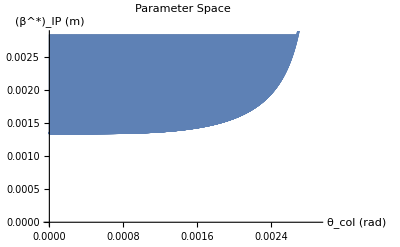

```mathematica
(*Plot β-θ Space for a single case*)
ListPlot[Transpose[{Arr[[nBW,1,All]],Arr[[nBW,2,All]]}],AxesLabel->{"θ_col (rad)","(β^*)_IP (m)"},PlotLabel->"Parameter Space",Filling->Top]
```

```mathematica
(*Plot β-θ Space for all cases*)
ListLinePlot[Table[Transpose[{Arr[[i,1,All]],Arr[[i,2,All]]}],{i,nBW}],AxesLabel->{"θ_col (rad)","(β^*)_IP (m)"},PlotLabel->"Parameter Space",PlotLegends->Table[ToString[f[i,4,1]*100]<>"%",{i,nBW}]]
```

-Graphics-

## Finding F_ψ Maximised Values + Saving

```mathematica
(*Eta Array for Subscript[F, ψ] and BW maxes*)
Arr2=Array[η,{2,nBW}];
```

```mathematica
(*Zeta array for θ and β maxes*)
Arr3=Array[ζ,{2,nBW}];
```

```mathematica
(*Get BW Subscript[F^MAX, ψ] θ and β for this maximum*)
For[α=0,α<nBW,α++,
maxindex = Position[Arr⟦α+1⟧⟦3⟧,Max[Arr⟦α+1⟧⟦3⟧⟦1;;endpoint[α+1]⟧](*⟦1⟧*)]⟦1,1⟧;
(* BW, Flux, Angle, Beta*)
η[1,α+1]=f[α+1,4,maxindex];
η[2,α+1]=f[α+1,3,maxindex];
ζ[1,α+1]=f[α+1,1,maxindex];
ζ[2,α+1]=f[α+1,2,maxindex];
];
(*Function to tell when this is over*)
(*Get["GetNameFunction"];
SpeakName;*)
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Saving the Arrays*)
SetDirectory[NotebookDirectory[]];
Arr2>>"CBETATuningData/CBETA150FBW_FINAL.txt"
Arr3>> "CBETATuningData/CBETA150BT_FINAL.txt"
```

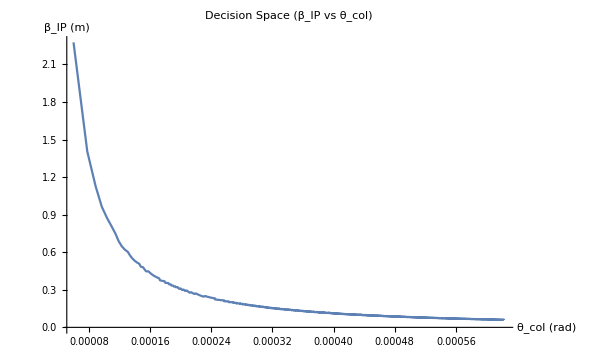

```mathematica
(*Maximum Points in the Parameter Space*)
ListLinePlot[ Transpose[Arr3],AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Decision Space (β_IP vs θ_col)",PlotRange->All]
```

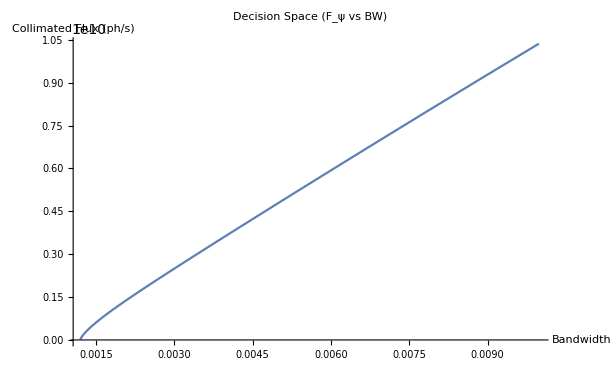

```mathematica
(*Plotting the Decision Space*)
ListLinePlot[ Transpose[Arr2],AxesLabel->{"Bandwidth","Collimated Flux (ph/s)"},PlotLabel->"Decision Space (F_ψ vs BW)",PlotRange->All]
```

# Multiple Case Plots (F_ψ-ΔE_x/E_x)

```mathematica
(*Using multiple cases to create β-θ Maximum plots*)
SetDirectory[NotebookDirectory[]];
CBETAβθ150=<<"CBETA150BetaTheta1to10.txt";
CBETAβθ114=<<"CBETA114BetaTheta1to10.txt";
CBETAβθ078=<<"CBETA078BetaTheta1to10.txt";
```

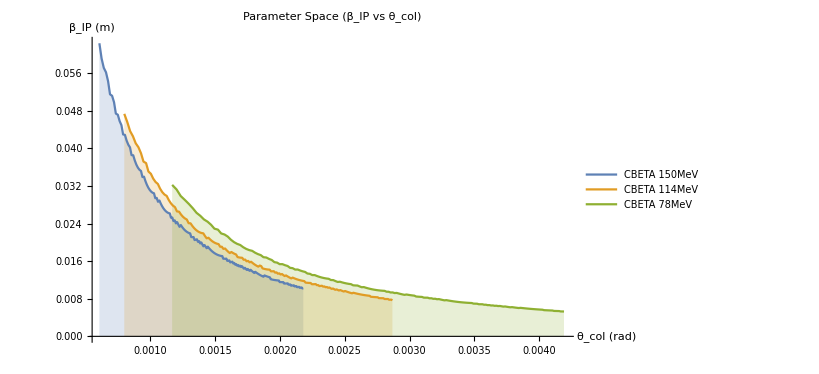

```mathematica
(*Plot*)
ListLinePlot[{Transpose[CBETAβθ150],Transpose[CBETAβθ114],Transpose[CBETAβθ078]},AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Parameter Space (β_IP vs θ_col)",PlotLegends->Placed[{"CBETA 150MeV","CBETA 114MeV","CBETA 78MeV"},{0.7,0.7}],PlotRange->All,Filling->Axis]
```

```mathematica
(*Using Multiple Cases to create Subscript[F, ψ]-BW plots*)
SetDirectory[NotebookDirectory[]];
CBETAFBW150=<<"CBETA150FBW1to10.txt";
CBETAFBW114=<<"CBETA114FBW1to10.txt";
CBETAFBW078=<<"CBETA078FBW1to10.txt";
```

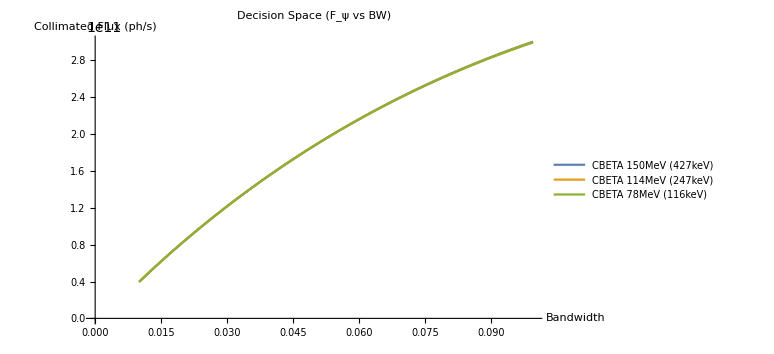

```mathematica
(*Plot*)
ListLinePlot[{Transpose[CBETAFBW150],Transpose[CBETAFBW114],Transpose[CBETAFBW078]},AxesLabel->{"Bandwidth","Collimated Flux (ph/s)"},PlotLabel->"Decision Space (F_ψ vs BW)",PlotLegends->Placed[{"CBETA 150MeV (427keV)","CBETA 114MeV (247keV)","CBETA 78MeV (116keV)"},{0.8,0.3}]]
```

# Single Case Calculations

## F_ψ Maximised Values (β-θ) for a Given Bandwidth

```mathematica
(*Trial Bandwidth*)
BW=0.1*1/100;
```

```mathematica
(*Storage Array*)
Arrsing=Array[υ,{3,npoints}];
```

```mathematica
For[i=0,i<npoints,i++,
θ=i*step;
β=Sqrt[T[γ,ϵn]^2/(BW^2-(ψ[θ,γ]^4/((B[γ,Elaser] +P*ψ[θ,γ]^2)^2))-((1+Y[γ,Elaser])/(Y[γ,Elaser]+ψ[θ,γ]^2))^2*EbSpread^2-((1+ψ[θ,γ]^2)/(Y[γ,Elaser]+ψ[θ,γ]^2))^2*ELSpread^2)]/.trialcase;

(*Break Condition to stop imaginary β*)
If[β==Re[β],
υ[1,i+1]=θ;
υ[2,i+1]=β;
υ[3,i+1]=G[γ,Elaser,Q,Epulse,rep,ϕ]/(Sqrt[K[γ,ϵn]*β+J[σL]]*Sqrt[R[ϕ]*(K[γ,ϵn]*β+J[σL])+H[σz,tpulse,ϕ]])*(ψ[θ,γ]^2+L[γ,Elaser]*ψ[θ,γ]^4)/(1+(M[γ,Elaser]+1)*ψ[θ,γ]^2+M[γ,Elaser]*ψ[θ,γ]^4)/.trialcase;
υend=i+1;,
υend=i;
Break[];
];
];
```

```mathematica
(*Calculation of maximum Values*)
maxsingindex = Position[Arrsing⟦3⟧,Max[Arrsing⟦3⟧⟦1;;υend⟧]]⟦1,1⟧;

Fψ = Max[Arrsing⟦3⟧⟦1;;υend⟧];
βmax = υ[2,maxsingindex];
θmax = υ[1,maxsingindex];

Print[Fψ];
Print[βmax];
Print[θmax];
```

4.09723×10^8

4.59954

23/1000000

## Maximum Peak Energy

```mathematica
Egam[γ_,Einc_]:=(4*γ^2*Einc)/(1+Xrec[γ,Einc]);
(*This misses off the angular contribution (γθ)^2, as assume we want the maximum and we don't have observation angles for anything*) 
Egam[γ,Elaser]/.trialcase
```

## Peak + Average Brilliance Calculation

```mathematica
(*The Brilliance calculations are still undergoing some work. These are rough but correct formulas appearing multiple times in the literature. I'm working on a better peak brilliance calc based on a F.V.Hartemann paper, but the mathematical detail of his papers make me wish I was in a vegatative state*)
```

```mathematica
(*Average Brightness*)
BAvg[γ_,ϵn_]:=(γ^2*Fψ)/(4*π^2*(ϵn*10^6)^2);
```

```mathematica
BAvg[γ,ϵn]/.trialcase
```

1.65391×10^14

```mathematica
(*Peak Brilliance, Exclude this for now*)
BPk[γ_,rep_,ϵn_,tpulse_]:=(γ^2*Fψ)/(4*π^2*rep*(ϵn*10^6)^2*tpulse);
```

```mathematica
BPk[γ,rep,ϵn,tpulse]/.trialcase
```

2.90159×10^17

## Spectral Density Calculation

```mathematica
(*Exclude this for now*)
SpecDen[γ_,Einc_]:=Fψ/(4*Sqrt[2*π]*γ^2*Einc*bw);
SpecDen[γ,Elaser]/.trialcase
```

8766.64

# Effect of Beam Energy Spread

## Main Calculation

```mathematica
(*Fixed Bandwidth Value*)
bw=0.5*1/100;
```

```mathematica
(*Arrays*)
Arr=Array[f,{nEb,4,npoints}];
Array[endpoint,{nEb}];
```

```mathematica
For[α=0,α<nEb,α++,
BeamSpread=Ebmin+α*Ebstep;
For[i=0,i<npoints,i++,
θ=i*step;
β=Sqrt[T[γ,ϵn]^2/(bw^2-(ψ[θ,γ]^4/((B[γ,Elaser] +P*ψ[θ,γ]^2)^2))-((1+Y[γ,Elaser])/(Y[γ,Elaser]+ψ[θ,γ]^2))^2*BeamSpread^2-((1+ψ[θ,γ]^2)/(Y[γ,Elaser]+ψ[θ,γ]^2))^2*ELSpread^2)]/.trialcase;
(*Break Condition to stop imaginary β*)
If[β==Re[β],
f[α+1,1,i+1]=θ;
f[α+1,2,i+1]=β;
f[α+1,3,i+1]=G[γ,Elaser,Q,Epulse,rep,ϕ]/(Sqrt[K[γ,ϵn]*β+J[σL]]*Sqrt[R[ϕ]*(K[γ,ϵn]*β+J[σL])+H[σz,tpulse,ϕ]])*(ψ[θ,γ]^2+L[γ,Elaser]*ψ[θ,γ]^4)/(1+(M[γ,Elaser]+1)*ψ[θ,γ]^2+M[γ,Elaser]*ψ[θ,γ]^4)/.trialcase;
f[α+1,4,i+1]=BeamSpread;
endpoint[α+1]=i+1;
,
endpoint[α+1]=i;
Break[];
];
];
];
```

## Parameter Space Plotting

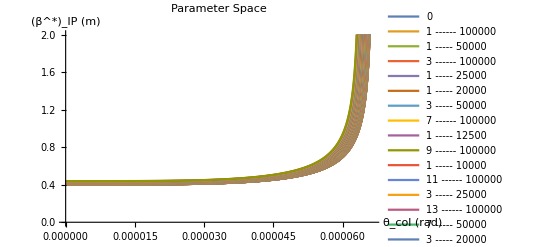

```mathematica
ListLinePlot[Table[Transpose[{Arr[[i,1,All]],Arr[[i,2,All]]}],{i,nEb}],AxesLabel->{"θ_col (rad)","(β^*)_IP (m)"},PlotLabel->"Parameter Space",PerformanceGoal->"Quality",PlotRange->{0,2},PlotLegends->Table[ToString[f[i,4,1]],{i,nEb}]]
```

## Finding F_ψ Maximised Values

```mathematica
(*Storage Arrays*)

(*Eta Array for Subscript[F, ψ] and EbSpread maxes*)
Arr2=Array[η,{2,nEb}];

(*Zeta array for θ and β maxes*)
Arr3=Array[ζ,{2,nEb}];
```

```mathematica
(*Get  Subscript[F^MAX, ψ] θ and β for this maximum EbSpread*)
For[α=0,α<nEb,α++,
maxindex = Position[Arr⟦α+1⟧⟦3⟧,Max[Arr⟦α+1⟧⟦3⟧⟦1;;endpoint[α+1]⟧](*⟦1⟧*)]⟦1,1⟧;
(* EbSpread, Flux, Angle, Beta*)
η[1,α+1]=f[α+1,4,maxindex];
η[2,α+1]=f[α+1,3,maxindex];
ζ[1,α+1]=f[α+1,1,maxindex];
ζ[2,α+1]=f[α+1,2,maxindex];
];
```

## Plotting

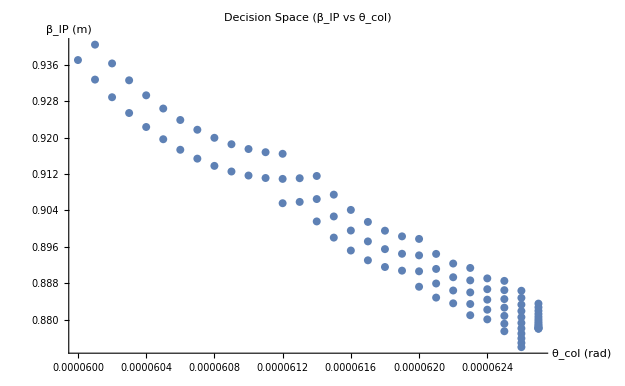

```mathematica
(*Maximum Points in the Parameter Space*)
ListPlot[ Transpose[Arr3],AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Decision Space (β_IP vs θ_col)",PlotRange->All]
```

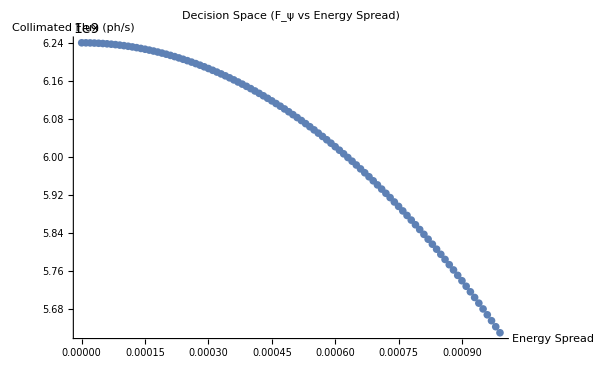

```mathematica
(*Plotting the Decision Space*)
ListPlot[ Transpose[Arr2],AxesLabel->{"Energy Spread","Collimated Flux (ph/s)"},PlotLabel->"Decision Space (F_ψ vs Energy Spread)"]
```

## Saving

```mathematica
SetDirectory[NotebookDirectory[]];
(*Arr2>>"case340FEbSpread.txt"
Arr3>> "case340BetaThetaEbSpread.txt"*)
```

# Multi Case Plots (F_ψ-ΔE_e/E_e)

## Multiple Energy Plot

```mathematica
SetDirectory[NotebookDirectory[]];
DIANAβθ1020=<<"case1020BetaThetaEbSpread.txt";
DIANAβθ680=<<"case680BetaThetaEbSpread.txt";
DIANAβθ340=<<"case340BetaThetaEbSpread.txt";
```

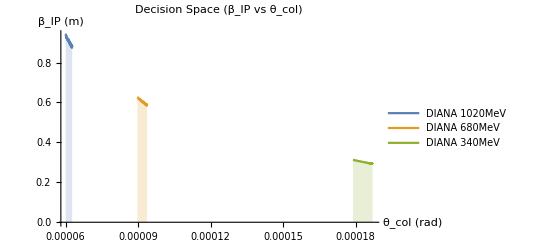

```mathematica
(*Plot*)
ListLinePlot[{Transpose[DIANAβθ1020],Transpose[DIANAβθ680],Transpose[DIANAβθ340]},AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Decision Space (β_IP vs θ_col)",PlotLegends->{"DIANA 1020MeV","DIANA 680MeV","DIANA 340MeV"},PlotRange->All,Filling->Axis]
```

```mathematica
(*Using Multiple Cases to create Subscript[F, ψ]-BW plots*)
SetDirectory[NotebookDirectory[]];
DIANAFEb1020=<<"case1020FEbSpread.txt";
DIANAFEb680=<<"case680FEbSpread.txt";
DIANAFEb340=<<"case340FEbSpread.txt";
```

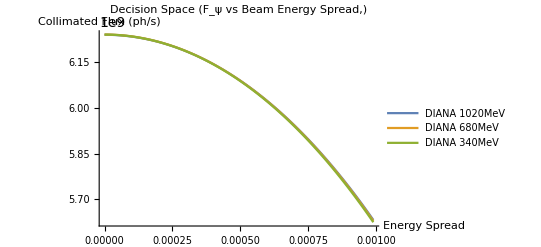

```mathematica
(*Plot*)
ListLinePlot[{Transpose[DIANAFEb1020],Transpose[DIANAFEb680],Transpose[DIANAFEb340]},AxesLabel->{"Energy Spread","Collimated Flux (ph/s)"},PlotLabel->"Decision Space (F_ψ vs Beam Energy Spread,)",PlotLegends->{"DIANA 1020MeV","DIANA 680MeV","DIANA 340MeV"}]
```